```mathematica
PRÀCTICA 4: INTEGRACIÓ
```

```mathematica
ACTIVITAT 1
```

```mathematica
f[x_]=(x-Sqrt[ArcTan[2x]])/(1+4x^2)
```

(x-√ArcTan[2 x])/(1+4 x^2)

```mathematica
Integrate[f[x],x]
```

-1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]

```mathematica
Per tant, una primitiva de f(x) és la funció -1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]
```

```mathematica
Integrate[f[x],{x,0,1}]
```

-1/3 ArcTan[2]^(3/2)+Log[5]/8

```mathematica
N[%]
```

-0.187138

```mathematica
Per tant, una aproximació de la integral definida que es demana és -0.187138
```

```mathematica
ACTIVITAT 2
```

```mathematica
f[x_]=Sin[x]/x
```

Sin[x]/x

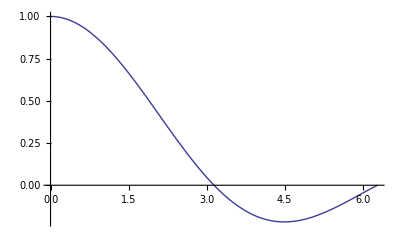

```mathematica
Plot[f[x],{x,0,2*Pi}]
```

```mathematica
Calculem l'abcissa del punt de tall de la gràfica amb l.b4.08eix OX. En aquest cas, és evident: x=π
```

```mathematica
Calculem l'àrea amb 2 integrals definides, tenint en compte el signe de la funció en cada subinterval:
```

```mathematica
NIntegrate[f[x],{x,0,Pi}]-NIntegrate[f[x],{x,Pi,2Pi}]
```

2.28572

```mathematica
També podem utilitzar valor absolut, si no volem tindre cura del signe:
```

```mathematica
Abs[NIntegrate[f[x],{x,0,Pi}]]+Abs[NIntegrate[f[x],{x,Pi,2Pi}]]
```

2.28572

```mathematica
ACTIVITAT 3
```

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=2x+1
```

1+2 x

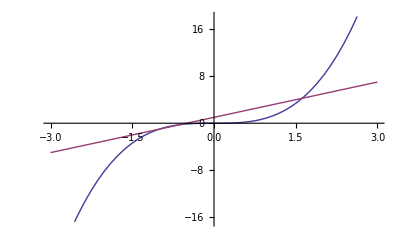

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

```mathematica
Sembla que les gràfiques de les dues funcions es tallen en 3 punts. De totes formes, podem representar la gràfica "al voltant" de la regió més difícil de veure:
```

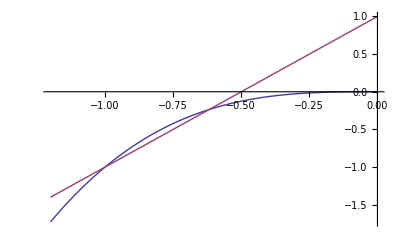

```mathematica
Plot[{f[x],g[x]},{x,-1.2,0}]
```

```mathematica
Calculem els tres punts de tall:
```

```mathematica
Solve[f[x]==g[x],x]
```

{{x→-1},{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
N[%]
```

{{x→-1.},{x→-0.618034},{x→1.61803}}

```mathematica
Calculem l'àrea en cadascuna de les dues regions determinades pels punts de tall, i les sumem:
```

```mathematica
Abs[Integrate[f[x]-g[x],{x,-1,1/2 (1-√5)}]]+Abs[Integrate[f[x]-g[x],{x,1/2 (1-√5),1/2 (1+√5)}]]
```

-11/8+(15 √5)/8

```mathematica
N[%]
```

2.81763

```mathematica
ACTIVITAT 4
```

```mathematica
f[x_]=Cos[x]/(x+1)
```

Cos[x]/(1+x)

```mathematica
NIntegrate[f[x],{x,0,1}]
```

0.601044

```mathematica
Copiem i activem la funció del fitxer FuncionsPredefinides.nb que aplica el mètode dels Trapezis:
```

```mathematica
Trapezis[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+2*Sum[f[a+k*h],{k,1,n-1}]+f[b])*h/2,20]]
```

```mathematica
Apliquem aquesta funció al nostre problema:
```

```mathematica
Trapezis[f,{0,1,10}]
```

0.60141412919716912939

```mathematica
El valor aproximat que hem obtingut és 0.60141412919716912939
```

```mathematica
Representem el valor absolut de la defivada segona de f(x) per trobar una cota superior a l'interval d'integració:
```

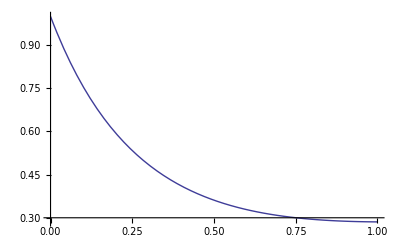

```mathematica
Plot[Abs[f''[x]],{x,0,1}]
```

```mathematica
Fixeu-vos que en la gràfica anterior els eixos no es tallen a l'origen (estan desplaçats). Açò ho fa Mathematica automàticament per a que la gràfica quede 'ben enquadrada'. Amb l'opció AxesOrigin podem fer que el punt de tall dels eixos siga l'origen:
```

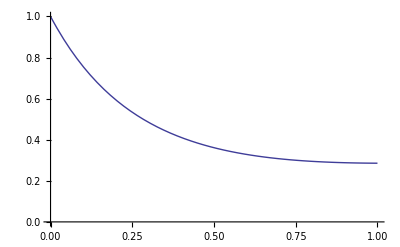

```mathematica
Plot[Abs[f''[x]],{x,0,1},AxesOrigin->{0,0}]
```

```mathematica
Veiem que la funció |f''(x)| és decreixent a l'interval [0,1]. Per tant, |f''(0)| serà la menor cota superior posible:
```

```mathematica
Abs[f''[0]]
```

1

```mathematica
Podem agafar, per tant, M_2=1
```

```mathematica
La cota de l'error és M_2 (b-a)^3/(12n^2):
```

```mathematica
1/(12*10^2)
```

1/1200

```mathematica
N[%]
```

0.000833333

```mathematica
És a dir, 8.3333*10^(-4)<10^(-3). Per tant, m=3 i podem asegurar que l'aproximació té 2 xifres decimals exactes (encara que, realment, en té 3)
```

```mathematica
ACTIVITAT 5
```

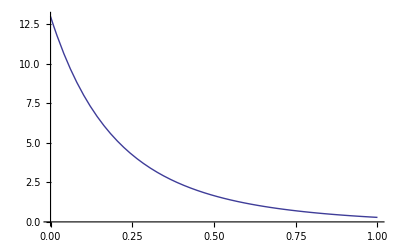

```mathematica
Plot[Abs[f''''[x]],{x,0,1}]
```

```mathematica
Veiem que la funció |f^iv(x)| és decreixent a l'interval [0,1]. Per tant, |f^(iv)(0)| serà la menor cota superior posible:
```

```mathematica
Abs[f''''[0]]
```

13

```mathematica
Podem agafar, per tant, M_4=13
```

```mathematica
Una cota de l'error comès es M_4(b-a)^5/(180n^4). En el nostre cas:
```

```mathematica
13/(180*n^4)
```

13/(180 n^4)

```mathematica
Com volem 10 xifres decimals exactes, volem que l'error siga menor que 10^-11
```

```mathematica
Resolem la inequació 13/(180 n^4)<10^-11:
```

```mathematica
Reduce[13/(180*n^4)<10^(-11),n]
```

n<-(100 √5 26^(1/4))/(√3)||n>(100 √5 26^(1/4))/(√3)

```mathematica
Com ens interessen valors de n NATURALS, la condició relevant és n>((100 √5 26^(1/4))/(√3)). Aproximem aquesta cota:
```

```mathematica
N[(100 √5 26^(1/4))/(√3)]
```

291.52

```mathematica
El primer nombre natural parell major que aquest valor es 292. Per tant, agafarem n=292 per aplicar la fórmula de Simpson:
```

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
Simpson[f,{0,1,292}]
```

0.6010443852566021759

```mathematica
Només com a comprovació, compararem aquest resultat amb el que retorna NIntegrate (agafant 20 dígits de precissió):
```

```mathematica
NIntegrate[f[x],{x,0,1},WorkingPrecision->20]
```

0.60104438525431562757

```mathematica
Veiem que, efectivament, les 10 primeres xifres decimals coincideixen.
```